# SIGHT-READING MUSIC GENERATOR

## Lola Obielodan & Sachi Barnaby

## I. Melody

```mathematica
(* Convert a list of notes into SoundNote so they can be played out loud. *)
toSound[noteLst_]:=Return[Sound[Table[SoundNote[noteLst⟦x⟧,0.5],{x,Length[noteLst]}]]]
```

## A) Make a Scale based on the Key

```mathematica
(* Build a scale depending on the key if major or minor. *) 
synthesizeScale[key_,Morm_]:=Return[Switch[Morm,"Major",makeScale[key,{2,2,1,2,2,2,1}],"Minor",makeScale[key,{2,1,2,2,1,2,2}]]]
```

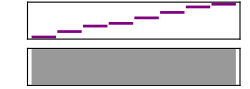

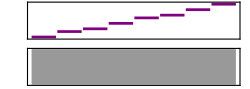

```mathematica
toSound[synthesizeScale[0,"Major"]]
toSound[synthesizeScale[-5,"Minor"]]
```

```mathematica
(* Make any scale with a given key and pattern. *)
makeScale[key_,pattern_]:=Module[{scalePattern=pattern,i=key,scaleLst={key},x=1},
While[i<key+12,
i+=scalePattern⟦x⟧;
AppendTo[scaleLst,i];
x++
];
Return[scaleLst]
]
```

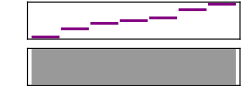

```mathematica
toSound[makeScale[-25,{3,2,1,1,3,2}]]
```

## B) Construct a Chord Progression based on the Scale

```mathematica
(* Info for sorting chords *)
majorChordsInMajorKey={1,4,5,8};
minorChordsInMajorKey={2,3,6};
dimChordsInMajorKey={7};

majorChordsInMinorKey={3,5,6,7};
minorChordsInMinorKey={1,4,8};
dimChordsInMinorKey={2};
```

Chord Construction:

```mathematica
(* To build chords, we can think of stacking thirds. A major third is 4 away, and a minor third is 3 away.  *)
(* Only major for us *)
buildMajorChord[root_]:={root,root+4,root+7};
```

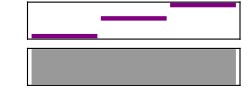

```mathematica
toSound[buildMajorChord[0]]
```

```mathematica
(* One minor chord please *)
buildMinorChord[root_]:={root,root+3,root+7};
```

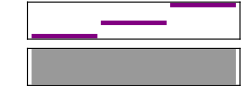

```mathematica
toSound[buildMinorChord[0]]
```

```mathematica
(* Build us a diminished chord! *)
buildDimChord[root_]:={root,root+3,root+6};
```

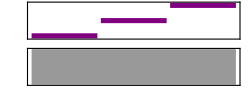

```mathematica
toSound[buildDimChord[0]]
```

Chord Progressions:

```mathematica
(* Now we need to be able to automatically call which chords are major and minor. *)
makeMajorChordProgression[scale_]:=Module[{i=1,chordLst={},chord},
While[i≤Length[scale],
If[MemberQ[majorChordsInMajorKey,i],chord=buildMajorChord[scale⟦i⟧]];
If[MemberQ[minorChordsInMajorKey,i],chord=buildMinorChord[scale⟦i⟧]];
If[MemberQ[dimChordsInMajorKey,i],chord=buildDimChord[scale⟦i⟧]];
AppendTo[chordLst,chord];
i++
];
Return[chordLst]
]
```

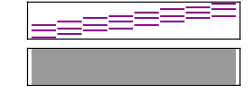

```mathematica
toSound[makeMajorChordProgression[synthesizeScale[0,"Major"]]]
```

```mathematica
(* This automatically produces major, minor, and diminished chords in a minor key. *)
makeMinorChordProgression[scale_]:=Module[{i=1,chordLst={},chord},
While[i≤Length[scale],
If[MemberQ[majorChordsInMinorKey,i],chord=buildMajorChord[scale⟦i⟧]];
If[MemberQ[minorChordsInMinorKey,i],chord=buildMinorChord[scale⟦i⟧]];
If[MemberQ[dimChordsInMinorKey,i],chord=buildDimChord[scale⟦i⟧]];
AppendTo[chordLst,chord];
i++
];
Return[chordLst]
]
```

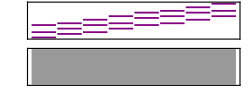

```mathematica
toSound[makeMinorChordProgression[synthesizeScale[0,"Minor"]]]
```

```mathematica
(* Create a chord progression based on given chords and their order. *)
realChordProgression[chordLst_,progressionLst_]:=Module[{i,newChordLst={}},
For[i=1,i≤Length[progressionLst],i++,
AppendTo[newChordLst,chordLst⟦progressionLst⟦i⟧⟧]
];
Return[newChordLst]
]
```

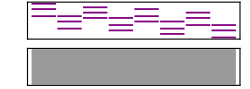

```mathematica
toSound[realChordProgression[makeMajorChordProgression[synthesizeScale[0,"Major"]],{8,4,7,3,6,2,5,1}]]
```

```mathematica
(* Use the scale in the key to make a major or minor chord progression, and put it in order. *)
constructChordProgression[key_,Morm_,chordProgressionOrder_]:=Module[{scale,chordProgression},
scale=synthesizeScale[key,Morm]; (* Create a scale to base the chords on. *)

chordProgression=Switch[Morm,
"Major",makeMajorChordProgression[scale],
"Minor",makeMinorChordProgression[scale]];

Return[realChordProgression[chordProgression,chordProgressionOrder]] (* Reorder the chords to our desired chord progression. *)
]
```

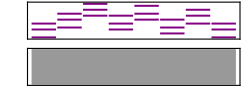

```mathematica
toSound[constructChordProgression[0,"Major",{1,4,7,3,6,2,5,1}]]
```

## C) Make a Melody

```mathematica
(* Add in neighbor tones as embellishments to the melody. *)
embellishedMelody[key_,Morm_,chordProgressionOrder_]:=Module[{melody,i,length},
melody=maintenanceMelody[constructChordProgression[key,Morm,chordProgressionOrder],synthesizeScale[key,Morm]]; (* Create a melody. *)

For[i=1,i<Length[melody],i++,
If[melody⟦i⟧==key-1||melody⟦i⟧==key+11,(* If the melody note is a leading tone, it must resolve up to the note of the key. *)
melody=Insert[melody,adjustNoteInterval[melody⟦i⟧,key],i+1]; (* Call adjustNoteInterval to find which octave of the key is closer to the note. *)
i++];

If[i+1<=Length[melody]&&SameQ[melody⟦i⟧,melody⟦i+1⟧], (* If a note is repeated, insert one or two neighbortones between the repetition. *)
melody=Insert[melody,neighborTones[melody⟦i⟧,key,Morm],i+1];
i++
]
];

Return[Flatten[melody]]
]
```

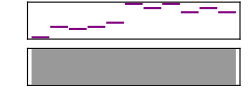

```mathematica
toSound[embellishedMelody[0,"Major",{1,4,7,3,6,2,5,1}]]
```

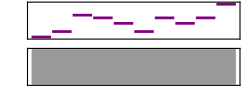

```mathematica
toSound[embellishedMelody[-25,"Minor",{1,5,6,1,4,2,5,1}]]
```

```mathematica
(* Make a melody that resolves correctly. *)
maintenanceMelody[chordProgression_,scale_]:=Module[{chords=chordProgression,melody,chordCnt,nextNote},
melody={chords⟦1,1⟧}; (* The first note of the melody should be the first note of the first chord. *)

For[chordCnt=2,chordCnt<Length[chords],chordCnt++,
nextNote=findNextNote[Last[melody],chords⟦chordCnt⟧,chords⟦chordCnt+1⟧,scale];
AppendTo[melody,nextNote]; (* Find a note that works in the melody, and add it. *)

If[Length[nextNote]>1,
chordCnt++; 
melody=Flatten[melody](* If multiple notes were added - note and resolution - flatten the melody out, and skip the next chord in the progression. *)
];
];
AppendTo[melody,adjustNoteInterval[Last[melody],scale⟦1⟧]]; (* Make sure the last note of the melody is the closest octave (of the scale's root) to the penultimate note. *)
Return[melody]
]
```

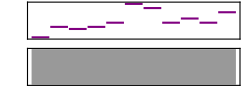

```mathematica
toSound[maintenanceMelody[constructChordProgression[0,"Major",{1,4,7,3,6,2,5,1}],synthesizeScale[0,"Major"]]]
```

```mathematica
(* Find the next note in the melody. *)
findNextNote[previousNote_,chord_,nextChord_,scale_]:=Module[{nextNote,workingChord=chord,interval,resolutionLst,resolution,chordOptions,niceNote=False},
While[niceNote==False, (* Run the loop until a nice note is found for the melody. *)
If[workingChord=={},Return[previousNote]]; (* If there are no more options in the chord for the next note, just repeat the previous note. *)
nextNote=RandomChoice[workingChord]; (* Pick a random note out of the chord. *)

workingChord=DeleteCases[workingChord,nextNote]; (* Take the next note choice out of the chord. *)

nextNote=octaveCheckWithLeaps[previousNote,nextNote]; (* Adjust the octaves of the interval as necessary. *)

interval=identifyInterval[previousNote,nextNote]; 
If[isLeap[previousNote,nextNote], (* If the interval is a leap, *)
If[interval⟦2⟧==1&&nextNote==scale⟦7⟧,Continue[]]; (* It is not allowed to leap up to the leading tone. *)

resolutionLst={nextNote-interval⟦2⟧,nextNote-interval⟦2⟧*2,nextNote}; (* Find resolution options, *)

chordOptions=addOctaves[nextChord]; (* And add octaves to the next chord. *)

resolution=Select[resolutionLst,MemberQ[chordOptions,#]&]; (* If any of the resolution options are in the next chord, return the next note and its resolution.  *)

If[resolution≠{},
If[resolution=={nextNote}, (* If the resolution is just a repeated note, put in a neighbor tone. *)
Return[{nextNote,resolutionInScale[resolutionLst⟦1⟧,resolutionLst⟦2⟧,scale],nextNote}];
niceNote=True, 

niceNote=True;
Return[{nextNote,First[resolution]}] (* If the resolution is not a repeated note, simply return the leaping note and its resolution. *)
]
],

niceNote=True;
Return[nextNote] (* If the interval is not a leap, return the new note. *)
];
]
]
```

```mathematica
findNextNote[0,buildMajorChord[5],buildMinorChord[2],synthesizeScale[0,"Major"]]
```

{5,4,5}

```mathematica
findNextNote[0,buildMajorChord[5],buildMinorChord[2],synthesizeScale[0,"Major"]]
```

0

```mathematica
(* Find the interval between two notes, and return the note that would have an interval less than an octave. *)
octaveCheckWithLeaps[note1_,note2_]:=Module[{firstInterval,octaveNote,newInterval},
firstInterval=identifyInterval[note1,note2];
If[firstInterval⟦1⟧<=10, (* If the interval is a step or leap less than a seventh, return the note. *)
Return[note2]
];

If[firstInterval⟦2⟧==1, (* If the interval is leaping up, take the second note down an octave. *)
octaveNote=note2-12,
octaveNote=note2+12 (* If the interval is leaping down, take the second note up and octave. *)
];

newInterval=identifyInterval[note1,octaveNote]; 

If[newInterval⟦1⟧<firstInterval⟦1⟧, (* If the new interval with the adjusted octave is smaller than the original interval, return the new note. *)
Return[octaveNote],
Return[note2]
]
]
```

```mathematica
octaveCheckWithLeaps[0,7]
```

7

```mathematica
octaveCheckWithLeaps[0,14]
```

2

```mathematica
(* Identify the interval amount and direction. *)
identifyInterval[note1_,note2_]:=Module[{intervalInfo,direction,interval},
interval=note2-note1;
If[interval<0,Return[{Abs[interval],-1}],Return[{interval,1}]]
]
```

```mathematica
identifyInterval[0,5]
```

{5,1}

```mathematica
identifyInterval[0,-12]
```

{12,-1}

```mathematica
(* Return true if the interval between two notes is a leap (a fourth or more). *)
isLeap[note1_,note2_]:=Return[TrueQ[Abs[note2-note1]≥5]]
```

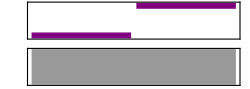

True

```mathematica
toSound[{0,5}]
isLeap[0,5]
```

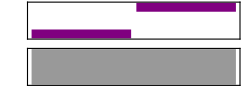

False

```mathematica
toSound[{0,3}]
isLeap[0,3]
```

```mathematica
(* Add the chords above and below an octave to the chord options. *)
addOctaves[chord_]:=Flatten[Table[{chord⟦x⟧,chord⟦x⟧-12,chord⟦x⟧+12},{x,Length[chord]}]]
```

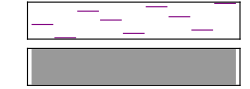

```mathematica
toSound[addOctaves[{0,4,7}]]
```

```mathematica
(* Check which of the resolution notes are in the key's scale. *)
resolutionInScale[note1_,note2_,scale_]:=Module[{neighbors},
If[MemberQ[scale,note1], (* If the first note is in the scale, return it. *)
Return[note1]
];
If[MemberQ[scale,note2], (* If the second note is in the scale, return it. *)
Return[note2]
];
Return[{}]
]
```

```mathematica
resolutionInScale[0,1,synthesizeScale[0,"Major"]]
```

0

```mathematica
(* Figure out which octave of the second note is closer to the first. *)
adjustNoteInterval[note1_,note2_]:=Module[{interval,adjustedNote},
If[Abs[note1-note2]>6, (* If the interval between the two notes is greater than 6, the second note can be adjusted octaves. *)
interval=identifyInterval[note1,note2];
adjustedNote=note2-12*interval⟦2⟧, (* Change the second note to an octave higher or lower depending on the leap direction. *)
adjustedNote=note2 (* If the leap distance is small, don't change the note. *)
];
Return[adjustedNote]
]
```

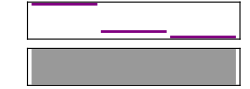

-2

```mathematica
toSound[{10,0,-2}]
adjustNoteInterval[0,10]
```

```mathematica
(* Produce extra tones above or below a given note to embellish a repeated sequence in the melody. *)
neighborTones[note_,key_,Morm_]:=Module[{scale,neighborNotes,position},
scale=DeleteDuplicates[Flatten[{synthesizeScale[key-12,Morm],synthesizeScale[key,Morm],synthesizeScale[key+12,Morm]}]];
(* Add a note before and after the scale so that the ends have neighbors. *)
position=Flatten[Position[scale,note]]; (* Find the position of the note in the scale. *)

(* Put these options in a list: one note above the given one, one note below, both with the one above first, and both with the one below first. *)
neighborNotes={scale⟦position-1⟧,scale⟦position+1⟧,{scale⟦position-1⟧,scale⟦position+1⟧},{scale⟦position+1⟧,scale⟦position-1⟧}};
Return[Flatten[RandomChoice[neighborNotes]]] (* Randomly pick one of the neighbor tone choices. *)
]
```

```mathematica
neighborTones[0,0,"Major"]
```

{2,-1}

```mathematica
neighborTones[9,0,"Major"]
```

{7}

## II. Rhythm

```mathematica
(* These rhythms are in order of: sixteenth, eighth, dotted eighth, quarter, dotted quarter, half, dotted half, and whole notes. *)
rhythmsInSimpleTime={0.25,1/3,0.5,2/3,0.75,1,1.5,2,3,4};
simpleProbability={15,10,15,5,12.5,20,12.5,10,7.5,7.5};

(* These rhythms are in order of: sixteenth, eighth, dotted eighth, quarter, dotted quarter, and dotted half notes. *)
rhythmsInCompoundTime={0.25,0.5,0.75,1,1.5,3};
compoundProbability={20,20,20,20,10,10};
```

```mathematica
(* Generate rhythms for one measure. *)
rhythmGenerator[beatType_,beatsPerBar_]:=Module[{rhythmLst={},rhythmChoice,chosenProbability,chosenRhythms,rhythmsRequired=beatsPerBar*beatType},
If[SameQ[beatType,1.5],(* The rhythm options and their probabilities depend on if its compound or simple. *)
chosenProbability=compoundProbability; chosenRhythms=rhythmsInCompoundTime,
chosenProbability=simpleProbability; chosenRhythms=rhythmsInSimpleTime
];

While[Total[rhythmLst]<rhythmsRequired,(* Run the loop until the number of beats created equals how many are needed in a measure. *)
rhythmChoice=beatCheck[RandomChoice[chosenProbability->chosenRhythms],beatType]; (* Pick a random rhythm and fill in the beat if necessary. *)

If[Total[rhythmLst]+Total[rhythmChoice]≤rhythmsRequired, (* If the picked rhythm fits in the measure, add it to the list. *)
AppendTo[rhythmLst,rhythmChoice];
rhythmLst=Flatten[rhythmLst];
];
];
Return[rhythmLst]
]
```

```mathematica
(* If the beat is starts with a note less than the total value needed for the beat, return rhythms that will fill up the rest of the beat. *)
beatCheck[downbeat_,beatType_]:=Module[{beatSpace,fillingChoice,fillingRhythm={}},
If[downbeat<beatType||(!IntegerQ[downbeat]&&downbeat≠beatType), (* If the beat has time left to fill after the downbeat, fill it. *)
beatSpace=Ceiling[downbeat]*beatType-downbeat; (* If the beat is being subdivided, determine how much time is left in the beat. *)

While[Total[fillingRhythm]<beatSpace,(* Run the loop until the beat is filled up. *)
If[MemberQ[{1/3,2/3},downbeat],fillingChoice=RandomChoice[{1/3,2/3}],fillingChoice=RandomChoice[{0.25,0.5,0.75,1}]]; (* Pick a subdivision value. If the downbeat is a triplet, it can only have a triplet set of options, and the other downbeats should not have triplet options. *)

If[fillingChoice+Total[fillingRhythm]≤beatSpace, (* If that values fits in the beat, add it to the list. *)
AppendTo[fillingRhythm,fillingChoice]
];
];
Return[Flatten[{downbeat,fillingRhythm}]],(* Return the first rhythm and the chosen filling ones. *)
Return[downbeat]] (* If the downbeat fills up the beat, return the downbeat. *)
]
```

```mathematica
(* The two numbers of the time signature correspond to the what kind of note represents the beat and how many beats are in a measure. *)
interpretTimeSignature[timeSignature_]:=Module[{beatType,beatsPerBar},
If[Last[timeSignature]==8,(* The bottom number corresponds to what kind of note represents the beat. *)

beatType=1.5; beatsPerBar=First[timeSignature]/3, (* If the bottom number is an 8, it's in compound time, so the dotted quarter note gets the beat, and by dividing the top number by 3, you get the number of beats per bar. *)

beatType=1;
If[Last[timeSignature]==2,
beatsPerBar=First[timeSignature]*2,
beatsPerBar=First[timeSignature] (* If the bottom number is a 4, it's in simple time, so the quarter note gets the beat, and the top number represent the number of beats in a bar. *)
]
];
Return[{beatType,beatsPerBar}]
]
```

## III. Combine Notes and Rhythms

#### Instrument Categories

```mathematica
(* These instruments can play and read in treble clef. *)
trebleInstrumentLst={"AltoSax","Banjo","BaritoneSax","Clarinet","EnglishHorn","Fiddle","Flute","FrenchHorn","Glockenspiel","Guitar","Harmonica","Oboe","Piccolo","Recorder","SopranoSax","TenorSax","Trumpet","Vibraphone","Viola","Violin","Woodblock","Xylophone"};

(* These instruments can play and read in bass clef. *)
bassInstrumentLst={"Bass","Bassoon","Cello","Contrabass","Trombone","Tuba"};

(* These instruments can read in either clef. *)
eitherLst={"Harp","Harpsichord","Marimba","Organ","Piano"};
```

#### Code

```mathematica
(* Depending on the level of sight-reading, add rests and correctly fill the measures. *)
toSoundWithLevels[level_,rhythmLst_,noteLst_,beatType_]:=Module[{melodyLst,leftoverLst},
If[SameQ[level,"Hard"]||SameQ[level,"Rhythm-only"],
melodyLst=insertRests[rhythmLst,noteLst,beatType], (* The Hard level should have rests interspersed. *)
melodyLst=Table[{noteLst⟦x⟧,rhythmLst⟦x⟧},{x,Length[noteLst]}] (* Easy and medium levels should match up the notes and rhythms to until there are no more notes. *)
];
(* If there are leftover rhythms, replace them with rests in the melody. *)
If[Length[melodyLst]<Length[rhythmLst],
leftoverLst=fillMeasure[rhythmLst,Length[melodyLst],beatType];
AppendTo[melodyLst,leftoverLst];
];
melodyLst=Partition[Flatten[melodyLst],2];
Return[melodyLst]
]
```

```mathematica
(* Convert the melody list into a sound file. *)
toSoundNote[melodyLst_, instrument_]:=Return[Sound[Table[SoundNote[melodyLst⟦x,1⟧,melodyLst⟦x,2⟧,instrument],{x,Length[melodyLst]}]]]
```

```mathematica
(* Create multiple measures of the hard level. *) (* Without toSoundNote *)
selectLevel[numOfMeasures_,level_,timeSignature_,key_,Morm_]:=Module[{rhythmLst,beatType,beatsPerBar,noteLst={},measureMelody,tries=1,chordProgression,i=1},
{beatType,beatsPerBar}=interpretTimeSignature[timeSignature];

If[SameQ[level,"Easy"],rhythmLst=Table[0.5,{x,2 * beatType * beatsPerBar*numOfMeasures}], (* Make enough eighth note rhythms to fill up the measures. *)
rhythmLst=Flatten[Table[rhythmGenerator[beatType,beatsPerBar],{x,numOfMeasures}]]]; (* Generate enough rhythms to fill up the measures. *)

If[SameQ[level,"Rhythm-only"],
noteLst=Table[key,Length[rhythmLst]*0.8+1]; (* For rhythm-only, there should not be a melody produced. *)
Return[{toSoundWithLevels[level,rhythmLst,noteLst,beatType],beatType}]
]; 

While[Length[noteLst]<Length[rhythmLst]&&tries≤3, (* Run the loop until melody list is as long as rhythm list or if it has unsuccessfully run 3 times. *)
measureMelody=embellishedMelody[key,Morm,chooseChordProgressionOrder[i]]; (* Call a chord progression a produce a possible melody increment. *)
If[Length[noteLst]+Length[measureMelody]≤Length[rhythmLst], (* If this increment fits into the measures, add it. *)
AppendTo[noteLst,measureMelody];
noteLst=Flatten[noteLst];
i++;
tries=0,
tries++ (* If the increment does not fit, it is not added, and tries is incremented to prevent an infinite loop. *)
]
];
Return[{toSoundWithLevels[level,rhythmLst,noteLst,beatType],beatType}] (* Call toSoundWithRhythm to combine the list and add rests as necessary. *)
]
```

```mathematica
(* Create a list of notes and rests according to the rhythm list. *)
insertRests[rhythmLst_,noteLst_,beatType_]:=Module[{numOfRests,i,melodyLst={{noteLst⟦1⟧,rhythmLst⟦1⟧}},restOrNote,soundBit,restCnt=0,noteCnt=2,restCheck=False,leftoverLst={},restLst},
numOfRests=Length[rhythmLst]-Length[noteLst];(* Calculate how many rests should be created by the difference between the lengths of the rhythm and note lists. *)

For[i=2,i≤Length[rhythmLst],i++,
If[noteCnt>Length[noteLst],
Break[](* If there are no more notes left, we should stop the loop. The rest of the rhythms will be combined into one rest. *)
];

If[restCnt<numOfRests,(* As long as we have not exceeded the allowed number of rests, we can randomly choose to include a rest. *)
If[restCheck,restOrNote="note",restOrNote=RandomChoice[{1,3}->{"rest","note"}]]; (* A rest should be chosen only if the previous rhythm was not a rest and only 1/4 of the time. *)

If[SameQ[restOrNote,"rest"], (* If a rest is chosen, produce one for the given length of time, change restCheck to True, and increment the rest count. *)
restCnt++;restCheck=True;
soundBit={None,rhythmLst⟦i⟧}, 

restCheck=False;
soundBit={noteLst⟦noteCnt⟧,rhythmLst⟦i⟧};noteCnt++ (* If a note is chosen, produce one for the given length of time and go to the next note. *)
],
soundBit={noteLst⟦noteCnt⟧,rhythmLst⟦i⟧};noteCnt++ (* If no more rests need to be made, make the rest of the rhythms notes. *)
];
AppendTo[melodyLst,soundBit];
];
Return[melodyLst]
]
```

```mathematica
(* If the melody runs out of notes before the last measure is filled, add rests to the end. *)
fillMeasure[rhythmLst_,i_,beatType_]:=Module[{leftoverLst,restLst={}},
leftoverLst=Table[rhythmLst⟦x⟧,{x,i+1,Length[rhythmLst]}]; (* Create a list of rhythms that are leftover after all the notes are called. *)

While[Mod[Total[leftoverLst],beatType]≠0,(* Until the leftover list is a set of combinable rhythms in the measure (divisible by beatType),*)
AppendTo[restLst,leftoverLst⟦1⟧];(* put the first rhythm of the leftoverLst into the restLst *)
leftoverLst=Drop[leftoverLst,1] (* and drop it from the leftoverLst. *);
];

restLst=DeleteCases[Sort[AppendTo[restLst,Total[leftoverLst]]],0]; (* Add the combined rests into restLst,sort the rests by smallest to largest, and delete any zeros. *)
Return[Table[{None,restLst⟦x⟧},{x,Length[restLst]}]] (* Return a list of lists with the rest rhythms. *)
]
```

```mathematica
(* Choose a chord progression to use in one measure. *)
chooseChordProgressionOrder[cnt_]:=Module[{options,randomOrder},
options={{4,7,3,6,2,5,1},{5,1},{6,2,5,1},{4,3,5,1},{2,5,6,4,1},{4,7,3,5,1}}; (* Here are the short chord progression options. *)

randomOrder=RandomChoice[{2,1,2,2,2,2}->options]; (* Pick one at random. *)

If[cnt==1,Return[PrependTo[randomOrder,1]],Return[randomOrder]] (* If it the first chord progression picked, it start with a I chord. *)
]
```

```mathematica
(* Generate music using the clef and vary the number of measures depending on the level. *) (* Without toSoundNote *)
generateMusic[key_,Morm_,timeSignature_,clef_,level_, instrument_]:=Module[{finalKey,numOfMeasures},
finalKey=interpretClef[clef,key,instrument]; (* Determine the octave of the key using the clef. *)
numOfMeasures=Switch[level,
"Rhythm-only",4,
"Easy",4,
"Medium",8,
"Hard",12]; (* Vary the number of measures with the level. *)
Return[selectLevel[numOfMeasures,level,timeSignature,finalKey,Morm]]
]
```

```mathematica
(* Keys in bass clef should start an octave lower than the keys in treble clef. *)
interpretClef[clef_,key_,instrument_]:=Module[{finalKey=key},
If[(SameQ[clef,2]&&(!MemberQ[trebleInstrumentLst,instrument]||MemberQ[eitherLst,instrument]))||MemberQ[bassInstrumentLst,instrument],finalKey-=24]; (* If the input is bass clef and the instrument can play in bass clef, take the key down an octave. *)
Return[finalKey]
]
```

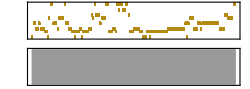

```mathematica
generateMusic[7,"Minor",{6,8},2,"Hard", "Oboe"]
```

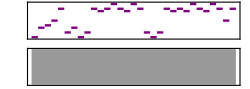

```mathematica
generateMusic[0,"Major",{4,4},1,"Easy", "Piano"]
```

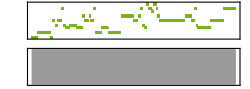

```mathematica
generateMusic[0,"Major",{4,4},2,"Medium", "Cello"]
```

## IV. Graphics

```mathematica
(* Import the treble clef and bass clef images. *)
SetDirectory[NotebookDirectory[]];
trebleClef=Import["Treble Clef.jpg"];
bassClef=Import["Bass Clef.jpg"];
downloadScreen=Import["Musescore Download Screen.png"];
dialog=Import["Dialog.png"];
```

Import::nffil: File Treble Clef.jpg not found during Import.

Import::nffil: File Bass Clef.jpg not found during Import.

Import::nffil: File Musescore Download Screen.png not found during Import.

Import::nffil: File Dialog.png not found during Import.

## A) Main Menu

```mathematica
(* Create the main menu with music customization options. *)
mainMenu[numForComputer_]:= DynamicModule[{keyNote=0,Morm="Major",treblePicture,bassPicture,x=50,y=45,clef=1,signature={4,4},level="Rhythm-only", instrument = "Piano",spacing},
treblePicture = Graphics[{White, Rectangle[{0, 0}, {x, y}], Inset [trebleClef, Center, Center, {x,y} ]}]; (* Inset the clef images into a background to regulate the size. *)
bassPicture= Graphics[{White, Rectangle[{0, 0}, {x, y}], Inset [bassClef, Center, Center, {x,y} ]}];
If[numForComputer==1,spacing=75,spacing=85]; (* The slider will need different spacing depending on the computer. *)

Column[{
(* Create a row with buttons for the key options and a toggler to switch between the Major and Minor option. *)
Row[{"What Key?:  ",SetterBar[Dynamic[keyNote],{ 0 -> " C ",7 -> " G ", 2 -> " D ", 9 -> " A ", 4 -> " E ", 11 -> " B ", 6-> " Gb ", 1 ->  " Db ", 8 -> " Ab ", 3 ->  " Eb ",  10 -> " Bb ", 5 -> " F "}],
 Toggler[Dynamic[Morm], {"Major" , "Minor"}]
},"  "], 

(* Create a row with buttons for time signature options and a toggler to switch between treble and bass clef options. *)
Row[{"What Time Signature?: ", SetterBar[Dynamic[signature], {{2, 2} -> " 2/2 ", {3, 4} -> " 3/4 ", {4, 4} -> " 4/4 ", {6, 8} -> " 6/8 "}], "   ",  "What Instrument?:", PopupMenu[Dynamic[instrument], {"AltoSax","Banjo","BaritoneSax","Bass","Bassoon","Cello","Clarinet","Contrabass","EnglishHorn","Fiddle","Flute","FrenchHorn","Glockenspiel","Guitar","Harmonica","Harp","Harpsichord","Marimba","Oboe","Organ","Piano","Piccolo","SopranoSax","TenorSax","Trombone","Trumpet","Tuba","Vibraphone","Viola","Violin","Woodblock","Xylophone"}], "   ",
"What Clef?:", Toggler[Dynamic[clef], {1->treblePicture,2->bassPicture}]}], 

(* Create a slider to choose a level of difficulty. *)
Row[{Column[{"Level of Difficulty: ",
Row[{
 Slider[Dynamic[level], {{{"Rhythm-only",35}, {"Easy",25},{"Medium",25},{"Hard",25}}}, ImageSize->Large]
},Right],
Row[{"rhythm-only", "easy", "medium", "hard"}, Spacer[spacing]]
}]}],

(* Create a button to open up a new window for the Generated Music Screen. *)
Button["Generate Music!", DialogReturn[CreateDialog[musicScreen[{keyNote, Morm, signature, clef, level, instrument},numForComputer]]], ImageSize->Medium]
},Center,Frame->All,Spacings->2, Background->White]
]
```

```mathematica
mainMenu[1]
```

```mathematica
(* Create a window for the mainMenu[] function. *)
runMainMenu[] :=Module[{},
filePath="";
Column[{
Row[{Button["Start Here for Windows!", DialogReturn[CreateDialog[Magnify[mainMenu[1],1.5], Background->LightPink]]],Button["Start Here for Mac!", DialogReturn[CreateDialog[Magnify[mainMenu[2],1.5],Background->LightPink]]]}, Spacer[10]],
InputField[Dynamic[filePath]]
},Center]
]
```

```mathematica
{runMainMenu[],Dynamic[filePath]}
```

{Start Here for Windows!Start Here for Mac!
,}

## B) Sheet Music Screen

```mathematica
(* Tailor the tempo to user specifications. *)
tailorTempo[tempo_,melodyInfo_]:=Module[{melodyLst,beatType},
{melodyLst,beatType}=melodyInfo;
Return[Map[{First[#],Last[#]*60/tempo/beatType}&,melodyLst]]
]
```

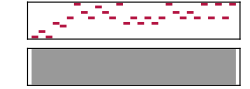

```mathematica
toSoundNote[tailorTempo[80,generateMusic[0,"Major",{4,4},1,"Easy","EnglishHorn"]],"EnglishHorn"]
```

```mathematica
(* Create a screen with a row of buttons on top, tempo input, and generated sheet music. *) 
musicScreen[options_,numForComputer_]:= DynamicModule[{key, Morm, timeSignature, clef, level, music, sheetMusic, instrument,tempo=60,beatType},
{key, Morm, timeSignature, clef, level, instrument}=options;
 (* Generate a sound file of music using user specifications. *)
music=generateMusic[key, Morm, timeSignature, clef, level, instrument];
sheetMusic = whichComputer[numForComputer,toSoundNote[First[music],instrument]]; (* Depending on the computer, create sheet music with Musescore. *)
Column[{
Row[{ Button["Generate New Music", {music = generateMusic[key, Morm, timeSignature, clef, level, instrument], sheetMusic = whichComputer[numForComputer,toSoundNote[First[music],instrument]]}], (* Create a button for generating more music using the same specifications. *)
Row[{Button["Play", AudioPlay[toSoundNote[tailorTempo[tempo,music],instrument]]], Button["Stop", AudioPause[]]}, Spacer[10]], (* Create buttons to start and stop audio of the music. *)
Button["Return to Main Menu", DialogReturn[CreateDialog[Magnify[mainMenu[numForComputer],1.5], Background->LightPink]]] (* Create a button to close this window and open up the main menu one. *)
}, Spacer[135]],
Row[{"Tempo:" ," ",InputField[Dynamic[tempo],Number]}],
Dynamic@First[sheetMusic]
},Alignment->Center]
]
```

```mathematica
musicScreen[{0,"Minor",{6,8},1,"Easy","Oboe"},1]
```

```mathematica
(* Call the correct function for sheet music depending on the type of computer used. *)
whichComputer[numForComputer_,music_]:=If[numForComputer==1,Return[sheetMusicForWindows[music]],Return[sheetMusicForMac[music]]];
```

## C) Start Screen

```mathematica
(* The start screen has instructions for downloading Musescore. *)
startScreen[]:=Module[{computerType},
Column[{"Please read all the instructions carefully. In order for our code to run correctly, you must download Musescore 3.",
Row[{"Here is the link for the download:", " ",Hyperlink[ "https://musescore.org/en/download"]}],
"",
"For Windows computers:",
"When you begin the download, follow the instructions on the Installation Wizard.",
"On the screen shown below to the left(third screen in the Wizard), copy the file path listed (highlighted in the red box), and input it", "into the white bar at the bottom of this screen with quotes (such as \"C:\\Program Files\\MuseScore 3\\\"). If a Mathematic dialog", "appears (shown below to the right), press Yes. Hit Enter to input your file location. Then complete your download.",
"Make sure to save this line somewhere as you will need it whenever you restart this program.",
Row[{"",Magnify[downloadScreen,4],Magnify[dialog,3]},Spacer[15]],
"         ",
"For Macs:",
"As of right now, it does not appear that Musescore 3 can be verified on Mac.", 
	"However, the code works for Musescore 2 which can be downloaded following the \"Older versions\" link on the downloads page.", 
"Click \"macOS 10.7 or higher\" for your download.",

"         ",

 Row[{" ",
runMainMenu[]
}, Spacer[200]]
}]
]
```

```mathematica
startScreen[]
```

Please read all the instructions carefully. In order for our code to run correctly, you must download Musescore 3.
Here is the link for the download: https://musescore.org/en/download

For Windows computers:
When you begin the download, follow the instructions on the Installation Wizard.
On the screen shown below to the left(third screen in the Wizard), copy the file path listed (highlighted in the red box), and input it
into the white bar at the bottom of this screen with quotes (such as "C:\Program Files\MuseScore 3\"). If a Mathematic dialog
appears (shown below to the right), press Yes. Hit Enter to input your file location. Then complete your download.
Make sure to save this line somewhere as you will need it whenever you restart this program.
-Graphics--Graphics-
         
For Macs:
As of right now, it does not appear that Musescore 3 can be verified on Mac.
However, the code works for Musescore 2 which can be downloaded following the "Older versions" link on the downloads page.
Click "macOS 10.7 or higher" for your download.
         
 Start Here for Windows!Start Here for Mac!

```mathematica
(* Run the start screen. *)
runStartScreen[]:= Button["Start Here", CreateDialog[startScreen[]]]
```

```mathematica
runStartScreen[]
```

Start Here

## D) Using Musescore

```mathematica
(* Use Musescore to return sheet music from a MIDI file. *)
sheetMusicForWindows[music_]:=Module[{},
If[!StringQ[filePath],filePath=ToString[filePath]]; (* If the user did not use quotes for their filePath, convert filePath into a string. *)
Export["music.mid",music];
RunProcess[{StringJoin[filePath,"bin\\MuseScore3.exe"],"music.mid","-o","music.pdf"}];
Return[Import["music.pdf"]];
]
```

```mathematica
(* Parameters should be the select level options. *)
sheetMusicForMac[music_]:=Module[{},
Export["music.mid",music];
RunProcess[{"/Applications/MuseScore\ 2.app/Contents/MacOS/mscore","music.mid","-o","music.pdf"}];
Return[Import["music.pdf"]]
]
```

This example only works on Windows computers.

```mathematica
sheetMusicForWindows[toSoundNote[First[selectLevel[4,"Medium",{6,8},1,"Major"]],"Oboe"]]
```

{-Graphics-}

This example only works for Macs.

```mathematica
sheetMusicForMac[toSoundNote[First[selectLevel[4,"Medium",{6,8},-13,"Minor"]],"Cello"]]
```

{-Graphics-}

## V. Demos

```mathematica
(* Uses specifications to create an audio file of a generated melody. *)
demoCode[key_,Morm_,timeSignature_,clef_,level_,instrument_]:=Module[{melody},
melody=First[generateMusic[key,Morm,timeSignature,clef,level,instrument]];
Return[toSoundNote[melody,instrument]]
]
```

## A) For the Main Menu:

```mathematica
runStartScreen[]
```

Start Here

## B) For making a melody:

This is a melody in C Major.

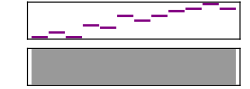

```mathematica
toSound[embellishedMelody[0,"Major",{1,4,7,3,6,2,5,1}]]
```

This is a melody in A minor.

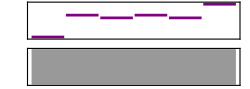

```mathematica
toSound[embellishedMelody[-3,"Minor",{1,6,2,5,1}]]
```

## C) For making rhythms:

The rhythmGenerator function produces a random list of rhythms. The first example is for 4/4 time, and the second example is for 6/8 time.

```mathematica
rhythmGenerator[1,4]
```

{1.5,0.5,1,0.25,0.25,0.25,0.25}

```mathematica
rhythmGenerator[1.5,2]
```

{0.25,1,0.25,0.25,0.5,0.5,0.25}

Our Rhythm-only level demonstrates how different rhythms are produced and how rests are inserted. The first example is in 4/4 time while the second example is in 6/8 time.

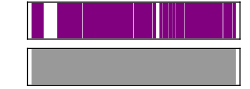

```mathematica
demoCode[-3,"Major",{4,4},1,"Rhythm-only","Piano"]
```

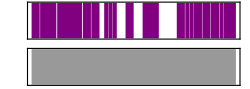

```mathematica
demoCode[-3,"Major",{6,8},1,"Rhythm-only","Piano"]
```

## D) For different levels of melodies:

These examples show our different levels. The first one is Easy in G Minor; the Easy level has no varying rhythms. This example is in 4/4 time in treble clef on oboe.

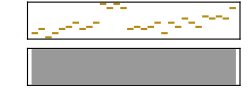

```mathematica
demoCode[7,"Minor",{4,4},1,"Easy","Oboe"]
```

This second one is the Medium level in F Major (3/4 time, bass clef, and tuba); the Medium level has varying notes and rhythms but no rests (unless some are needed at to fill up the last measure).

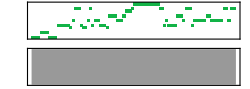

```mathematica
demoCode[7,"Major",{3,4},2,"Medium","Tuba"]
```

This last one is the Hard level in Eb Minor, and the Hard level has varying notes and rhythms along with rests. This example also has the customization of treble clef, 6/8 time, and violin.

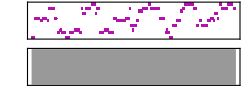

```mathematica
demoCode[3,"Minor",{6,8},1,"Hard","Violin"]
```

## E) Sheet music for different computers

This example only works on Windows computers.

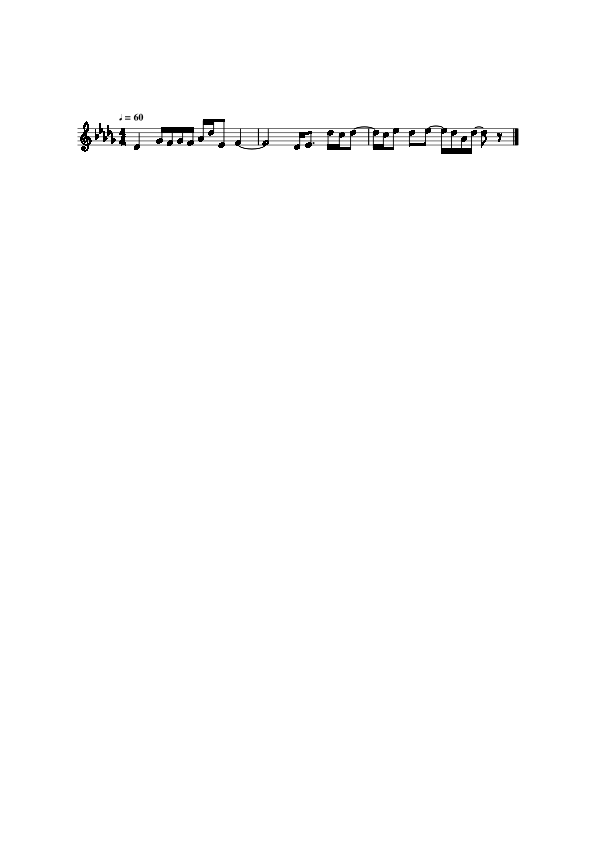

```mathematica
sheetMusicForWindows[toSoundNote[First[selectLevel[4,"Medium",{6,8},1,"Major"]],"Oboe"]]
```

This example only works for Macs.

```mathematica
sheetMusicForMac[toSoundNote[First[selectLevel[4,"Medium",{4,4},-13,"Minor"]],"Cello"]]
```

{-Graphics-}